Task 2

```mathematica
inFile = StringJoin[NotebookDirectory[], "input.txt"]
fileStream = OpenRead[inFile]
Is =Read[fileStream,{Word,Number}][[2]]
Us =Read[fileStream,{Word,Number}][[2]]
Ulist = ReadList[fileStream, Expression, Us]
Edges = Table[Ulist[[i, 1]]->Ulist[[i, 2]],{i, Us}]
Intences = Table[StringSplit[weights[[1]],{"/*","*/","b_"}][[1]]-> weights[[2]],{weights,ReadList[fileStream, {Word, Number}]}]
Print["|I|=",Is, " |U|=",Us]
Print["Edges: ",Edges]
Print["{Vertex, Weigth}: ",Intences]
```

C:\Users\Vitaly\Documents\Wolfram Mathematica\GraphAlgos\input.txt

InputStream[…]

7

13

{{1,3},{1,5},{2,1},{2,6},{3,6},{4,3},{5,2},{5,6},{6,1},{6,4},{7,3},{7,1},{7,5}}

{1->3,1->5,2->1,2->6,3->6,4->3,5->2,5->6,6->1,6->4,7->3,7->1,7->5}

{1→7,2→4,8→3,3→-1,6→-1,4→-7,11→-14,5→-2,7→6,9→-2,10→4,12→-9,13→1}

|I|=7 |U|=13

Edges: {1->3,1->5,2->1,2->6,3->6,4->3,5->2,5->6,6->1,6->4,7->3,7->1,7->5}

{Vertex, Weigth}: {1→7,2→4,8→3,3→-1,6→-1,4→-7,11→-14,5→-2,7→6,9→-2,10→4,12→-9,13→1}

Task 3

{GraphLayout→CircularEmbedding,VertexSize→0.4,VertexLabels→Placed[Name,Center]}

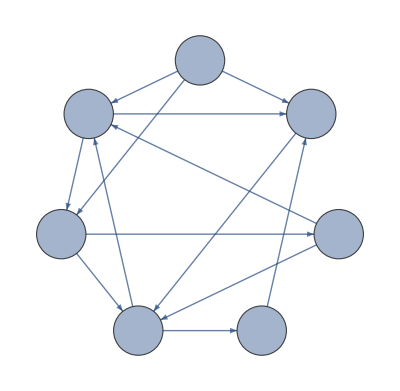

```mathematica
graphStyle = {GraphLayout->"CircularEmbedding", VertexSize->0.4,  VertexLabels->Placed["Name", Center]}
Graphing = Graph[Edges, graphStyle]
```

Task 4

```mathematica
weights =StringSplit[ToString[Intences[[#]]],{"->" }][[1]]&/@Range[Is]
OutTable = Total[Subscript[x, #]&/@EdgeList[Edges, #->_]]&/@Range[Is]
InTable = Total[Subscript[x, #]&/@EdgeList[Edges, _->#]]&/@Range[Is]
equations = OutTable - InTable
system = equations[[#]]==weights[[#]]&/@Range[Is]
system//MatrixForm
```

{1 ,2 ,8 ,3 ,6 ,4 ,11 }

{x_(1->3)+x_(1->5),x_(2->1)+x_(2->6),x_(3->6),x_(4->3),x_(5->2)+x_(5->6),x_(6->1)+x_(6->4),x_(7->1)+x_(7->3)+x_(7->5)}

{x_(2->1)+x_(6->1)+x_(7->1),x_(5->2),x_(1->3)+x_(4->3)+x_(7->3),x_(6->4),x_(1->5)+x_(7->5),x_(2->6)+x_(3->6)+x_(5->6),0}

{x_(1->3)+x_(1->5)-x_(2->1)-x_(6->1)-x_(7->1),x_(2->1)+x_(2->6)-x_(5->2),-x_(1->3)+x_(3->6)-x_(4->3)-x_(7->3),x_(4->3)-x_(6->4),-x_(1->5)+x_(5->2)+x_(5->6)-x_(7->5),-x_(2->6)-x_(3->6)-x_(5->6)+x_(6->1)+x_(6->4),x_(7->1)+x_(7->3)+x_(7->5)}

{x_(1->3)+x_(1->5)-x_(2->1)-x_(6->1)-x_(7->1)==1 ,x_(2->1)+x_(2->6)-x_(5->2)==2 ,-x_(1->3)+x_(3->6)-x_(4->3)-x_(7->3)==8 ,x_(4->3)-x_(6->4)==3 ,-x_(1->5)+x_(5->2)+x_(5->6)-x_(7->5)==6 ,-x_(2->6)-x_(3->6)-x_(5->6)+x_(6->1)+x_(6->4)==4 ,x_(7->1)+x_(7->3)+x_(7->5)==11 }

(x_(1->3)+x_(1->5)-x_(2->1)-x_(6->1)-x_(7->1)==1 
x_(2->1)+x_(2->6)-x_(5->2)==2 
-x_(1->3)+x_(3->6)-x_(4->3)-x_(7->3)==8 
x_(4->3)-x_(6->4)==3 
-x_(1->5)+x_(5->2)+x_(5->6)-x_(7->5)==6 
-x_(2->6)-x_(3->6)-x_(5->6)+x_(6->1)+x_(6->4)==4 
x_(7->1)+x_(7->3)+x_(7->5)==11 )